## Computing for Mathematical Physics 2022/23

# Homework 4

# Mark for homework 4: 38/42 (to be competed by your marker)

# Feedback from marker: (to be competed by your marker) Q1 16/20 : Marks lost here were for not labelling axes in plots, which you can easily do (and you may well need these in e.g. an exam). Please see my comments under the various bits of this question for more info and help. In particular, make sure you are also comfortable ending Which[...] functions with a if-all-the-above-fails condition + return value, of the form “... , True, BlahBlah ] ” (See my alternative to your hitQ in Q1b for an example of this.) Q2 8/8 Good. Solid. Please see my comments under Q2a though, in relation to Which[...] again. Q3 10/10 Good effort on a question that tripped a lot of people up. Very few people I marked got this right. See my comment under Q3c for a slightly simpler version of the code there (your code is nevertheless perfectly correct though). Q4 4/4 Nice to see this one come out confidently.

# Give your answers in the code cells marked (* Enter your solution here *)

Double click the vertical braces on the RHS of each of the question headings to open and view them.

1. Monte Carlo integration procedure to estimate π.  [20 marks]

a) Use Table and RandomReal to make a list of 100,000 points, called, shots, each one in the form of a two-element list {x,y}, with x values in the range -1 ≤ x ≤ 1 and y values in -2 ≤ y ≤ 2. You must use a semi-colon to terminate the Table command, to avoid filling the screen with 200,000 random numbers. Use ListPlot with option AspectRatio→Automatic, together with any other due formatting, to display the points.
[6 marks]

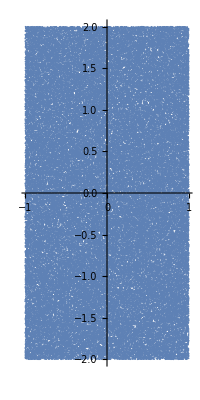

```mathematica
(*Create large list containing two inner lists*)
shots = Table[{RandomReal[{-1,1}],RandomReal[{-2,2}]}, 100000];
ListPlot[shots, AspectRatio->Automatic]
```

Q1a 4/6
• Got the basics right.
• Forgot to label axes though — question asks for ‘any other due formatting’.

b) Write a function hitQ, using Which, that specifically takes a two element list, {x,y}, as input. If x^2+y^2≤1, the function should return True, and False otherwise.
[4 marks]

```mathematica
(*Create delayed function whicb checks if point lies in the circle *)
hitQ[x_ ] := Which[x[[1]]^2+x[[2]]^2≤1, True,x[[1]]^2+x[[2]]^2>1, False ]
```

Q1b 4/4
•  Good.  Correct.
• The following would also work.
 hitQ[{x_,y_}]:=
Which[
(* If x^2+y^2≤1 we are expected to return True.     *)
x^2+y^2≤1,True,
(* If none of the other conditions above return   *)
(* True, i.e. if x^2+y^2>1 we return False.         *)
True,False
]
• Basically the Which[...] function checks each conditional inside it, in order, one at a time, until it finds one that evaluates to True, and when it does, it returns whatever is on the RHS of that conditional as the answer. So, by having a “True” sitting right at the end of each Which[...] command we are basically saying, “this last thing at the very end is what we should return if all conditionals above it have failed”. I.e. the last “ Which[..., ...,  True, Blah] ”  bit of any Which[...] command is like a final “if all else fails return Blah” catch. Ask me in class if you’d like a face-to-face explanation of this. It’s important that you are comfortable with how Which[...] works.

c) Use Select with hitQ to generate a new list called hitList, comprised of those points inside shots with  x^2+y^2≤1. You must use a semi-colon to terminate the Table command, to avoid filling the screen with a few 10,000 random numbers. Use ListPlot with option AspectRatio→Automatic, together with any other due formatting, to view the hitList points.
[5 marks]

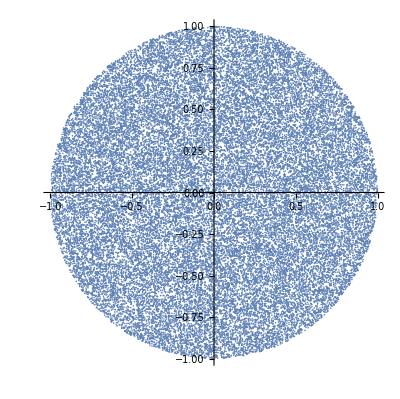

```mathematica
hitList = Select[shots, hitQ];
ListPlot[hitList, AspectRatio->Automatic]
```

Q1c 3/5
• Lost marks for not labelling any axes.

d) Compute the fraction of points inside shots with  x^2+y^2≤1, hitFraction.  
[1 mark]

```mathematica
hitFraction = Length[hitList] / Length[shots]
```

39109/100000

Q1d 1/1
• Good.

e) By considering hitFraction together with the initial area covered with the points in shots, determine a numerical estimate for π. Display your estimate to 5 s.f. For full marks in this part, you will need to list your logic, clearly, in 2-3 short sentences, in a text cell.
[4 marks]

Area of a circle is π r^2and area covered by the whole graph is 2r * 4r = 8 r^2. So fraction of area of circle to area of whole graph is π r^2/ 8 r^2 = π  / 8. So we can approximate the value of π by multiplying the ration of the area of the circle to the area of the whole graph by 8.

```mathematica
N[8 * hitFraction, 5]
```

3.1287

Q1e 4/4
• Right answer.

2. Recursive function. [8 marks]

Let the function P_n(x) be defined by the recursion relation:
	
	n P_n(x)   =   (2n-1)  x  P_(n-1)(x)  -  (n-1) P_(n-2)(x) 

with P_0(x)=1, P_1(x) = x.

a) Implement the function P_n(x) as a recursive function called PA[n_,x_] using Which.

```mathematica
(*Create function which has conditions for the first two numbers of the series*)
PA[n_, x_]:= Which [ n== 0, 1, n ==1, x, n>1, ((2n-1) x PA[n-1, x]-(n-1)PA[n-2, x])/n]
```

b) Implement the function P_n(x) again, now as PB[n_,x_], without using If or Which. Instead, carry out the implementation by providing three separate (overloaded) definitions for PB[n_,x_]:
i)   a definition specific to the n=0 case, PB[0,x_],
ii)  a definition specific to the n=1 case, PB[1,x_],
iii) a definition for all other general n values, PB[n_,x_].

```mathematica
(*Create normal function, then overload it*)
PB[n_, x_]:= ((2n-1)x PB[n-1, x]-(n-1)PB[n-2, x])/n
PB[0,x_]= 1;
PB[1,x_]:= x
```

c) Use Simplify together with the equal operator, ==, to test whether PA[15,x] and PB[15,x]equal Mathematica’s internal LegendreP[15,x] function. 
[8 marks]

```mathematica
Simplify[PA[15,x ]]== Simplify[LegendreP[15,x]]
(*Simplify both sides so that tehy are in the exact same format*)
Simplify[PB[15,x]] == Simplify[LegendreP[15,x]]
```

True

True

Nice.

Q2a 3/3
• Good. Perfectly correct.
• Again note, however, that instead of the last “ ... n>1, ((2n-1) x PA[n-1, x]-(n-1)PA[n-2, x])/n] ” in the Which[...] you could have had instead “ ... True, ((2n-1) x PA[n-1, x]-(n-1)PA[n-2, x])/n] ” . It would be good if  you could convince yourself, and get comfortable, with the latter way of doing things too, as it effectively amounts to saying “if none of the above were True, do this” , which is a very useful construct, that can come up in a lot of situations. In this particular case of Q2a, this means, make sure you are also comfortable with this minor modification of your answer:
	PA[n_, x_]:= Which [ n== 0, 1, n ==1, x, True, ((2n-1) x PA[n-1, x]-(n-1)PA[n-2, x])/n]

Q2b 3/3
• Nice. Solid.

Q2c 2/2
• Good.
• Would be slightly safer, in future questions, to wrap the whole expression inside Simplify[...] as in 
	Simplify[PA[15,x]==LegendreP[15,x]]
	Simplify [PB[15,x]==LegendreP[15,x]]
instead of what you have above.

3. List manipulation with user defined functions.  [10 marks]

For this question you will need to evaluate the following code cell to store the list marks in memory, corresponding to fictitious student exam marks.

```mathematica
marks={
{1,"Rishi","Sunak",13},
{2,"Donald","Trump",1},
{3,"Donald","Trump",0},
{3,"Rishi", "Sunak",17},
{1,"Liz","Truss",4},
{1,"Joe", "Biden",16},
{2,"Joe", "Biden",14},
{1,"Barak","Obama",22},
{1,"Theresa","May",17},
{2,"Liz","Truss",1},
{1,"Boris","Johnson"},
{2,"Theresa","May",11},
{2,"Boris","Johnson"},
{2,"Barak","Obama",25}
};
```

Each entry in the marks list has the form

	{test number, first name, family name, mark}

or, if a mark is missing,

	{test number, first name, family name} .

a) Write a function consolidate[data_], using Map and Rest, capable of taking in the list marks and removing the test number from the start of each entry. Apply your consolidate function to the list marks.
[2 marks]

```mathematica
(*Rest function removes first part of a list so apply to each part of the smaller lists. We don't need to specify level here as the map function already chooses the lowest level which is what we want*)
consolidate[data_]:= Map[Rest, data]
consolidate[ marks]
```

{{Rishi,Sunak,13},{Donald,Trump,1},{Donald,Trump,0},{Rishi,Sunak,17},{Liz,Truss,4},{Joe,Biden,16},{Joe,Biden,14},{Barak,Obama,22},{Theresa,May,17},{Liz,Truss,1},{Boris,Johnson},{Theresa,May,11},{Boris,Johnson},{Barak,Obama,25}}

Q3a 2/2
• Good!

b) Extend your  consolidate[data_] function so as to additionally apply a replacement rule to its output before it is returned. The replacement rule should act to consolidate the marks for each student, so that each student entry in the final output list is of the form

	{first name, family name, test1_mark, test2_mark,...}

I.e., the final output list should have only one member per student.

Each member of the final output list should only contain test marks for tests attempted by the student named in that member, i.e., each member may have a different length.

Apply this modified consolidate function to the list marks, and store the output as consolidatedMarks.
[4 marks]

```mathematica
consolidateRule = {a___, {b_, c_, d___},e___,{b_, c_, f___}, g___} ->{a,{b, c, d, f},e, g};
consolidatedMarks =consolidate[marks]//.consolidateRule
```

{{Rishi,Sunak,13,17},{Donald,Trump,1,0},{Liz,Truss,4,1},{Joe,Biden,16,14},{Barak,Obama,22,25},{Theresa,May,17,11},{Boris,Johnson}}

Q3b 4/4
• Nice to see you get this.

c) Define a function orderedFirstNamesQ[member1_,member2_] designed to take two members from the consolidatedMarks list as input. This function should, itself, use OrderedQ to determine whether member1 and member2 are input in alphabetical order, according to the first name contained within each one. If member1 and member2 have been input to the function in alphabetical order, as determined by examining the first name in each input member, orderedFirstNamesQ should return True, otherwise return False.

Use Sort together with the orderedFirstNamesQ function to rearrange the members of consolidatedMarks such that their first names appear in  alphabetical order.
[4 marks]

```mathematica
(*function takes in two names and determines whether the first names are in alphabetical order*)
orderedFirstNamesQ [x_,y_]:=If[OrderedQ[{x[[1]],y[[1]]}], True,False] 
Sort[consolidatedMarks, orderedFirstNamesQ]
```

{{Barak,Obama,22,25},{Boris,Johnson},{Donald,Trump,1,0},{Joe,Biden,16,14},{Liz,Truss,4,1},{Rishi,Sunak,13,17},{Theresa,May,17,11}}

Q3c 4/4
• Very well done. 
• Note that since OrderedQ is a function that by itself returns just True or False, you could have just had
OrderedQ[{x[[1]],y[[1]]}]
instead of 
If[OrderedQ[{x[[1]],y[[1]]}], True,False]

4. Pure functions.  [4 marks]

In this question we seek to compute a very basic numerical approximation to the integral of the function x^2 Cos[x]^2 over the range 0<=x<=3.5π, based on approximating the area under the function in this range by a number of thin rectangles, each of the same width.

Set rectangleWidths=0.00001;

Set rectangleUpperEdges=Range[rectangleWidths,3.5π,rectangleWidths];

a) Create a list of values, called rectangleHeights, by passing rectangleUpperEdges to Map, together with a pure function representation of x^2 Cos[x]^2. [I.e. if the i’th element in rectangleUpperEdges has a value, say, x_i, then the i’th element of rectangleHeights should have a value x_i^2 Cos[x_i]^2.] 
[2 marks]

```mathematica
rectangleWidths = 0.00001;
rectangleUpperEdges =  Range[rectangleWidths, 3.5 π, rectangleWidths];
```

```mathematica
rectangleHeights = Map[#^2 Cos[#]^2&, rectangleUpperEdges];
```

b) Create a list called rectangleAreas, by passing rectangleHeights to Map, together with a suitably defined pure function, to multiply each element in rectangleHeights by the constant rectangleWidths.
[1 mark]

```mathematica
rectangleAreas = Map[rectangleWidths #&, rectangleHeights];
```

c) Compute the sum of the elements in rectangleAreas, and compare it to what one obtains when one integrates x^2 Cos[x]^2 over 0<=x<=3.5π using Mathematica’s native Integrate function.
[1 mark]

```mathematica
N[Total[rectangleAreas], 10]
N[Integrate[x^2 Cos[x]^2,{x, 0, 3.5π}],10]
```

218.817

218.817

Answers are exactly the same, no further precision past 6 significant figures.

Q4 4/4
• Excellent. Well done!

Total marks available: 42

Solutions are due by 1200 noon on Thursday February 9th here:  allow time for uploading on moodle.

A 10% mark deduction will be made (4 marks) if the template isn’t used.

Name your solution notebook file in the format WK4_HMWK_<Initials>_<Family Name>.nb, e.g. WK4_HMWK_K_Hamilton.nb

Make a backup copy of your solutions.

Delete all cell evaluation output by selecting Cell → Delete All Output from the drop-down menus at the top of the screen, then save and upload that file to Moodle.

The first thing your marker will do when they receive your notebook is to evaluate all of it, to regenerate the output, by clicking Evaluation → Evaluate Notebook from the drop-down menus at the top of the screen. It is your responsibility to check that carrying out this process will produce the output you intend it to, before you upload your work.

K. Hamilton, J. Bhamrah, J. Underwood, L. McKemmish — UCL
Last revision 09:16 30 Nov 2022